```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\AvoidedQP\\implementation\\"],
SetDirectory["~/Documents/GitHub/AvoidedQP/implementation/"]
]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/implementation

```mathematica
getPlotData[qpds_]:=(
ks = Normal[DeleteDuplicates[qpds[Take,"momentum"]]];
kinds=PositionIndex[Normal[qpds[Take,"momentum"]]];
qpkds=Table[qpds[kinds[[it]]],{it,Length[kinds]}];
Bs=Normal[DeleteDuplicates[qpds[Take,"interaction"]]];
Binds=Table[PositionIndex[Normal[qpkds[[it]][Take,"interaction"]]],{it,Length[qpkds]}];

weightData=Table[
Table[(
qpSize=Normal[qpkds[[kt]][Take,"size"][Binds[[kt]][B]]];
qpWeight=Normal[qpkds[[kt]][Take,"weight"][Binds[[kt]][B]]];
Table[{1/qpSize[[it]],qpWeight[[it]]},{it,Length[qpSize]}]
),{B,Bs}],
{kt,Length[ks]}];
gapData=Table[
Table[(
qpSize=Normal[qpkds[[kt]][Take,"size"][Binds[[kt]][B]]];
qpWeight=Normal[qpkds[[kt]][Take,"gap"][Binds[[kt]][B]]];
Table[{1/qpSize[[it]],qpWeight[[it]]},{it,Length[qpSize]}]
),{B,Bs}],
{kt,Length[ks]}];
)
```

```mathematica
makePlots[qpds_]:=(
getPlotData[qpds];
linear=Table[Table[Fit[weightData[[kt,it,-3;;-1]],{1,x},x],{it,1,Length[weightData[[kt]]]}],{kt,Length[ks]}];
quadratic=Table[Table[Fit[weightData[[kt,it,-3;;-1]],{1,x,x^2},x],{it,1,Length[weightData[[kt]]]}],{kt,Length[ks]}];
pltStyle={Directive[Blue],Directive[Lighter[Darker[Green]]],Directive[Orange],Directive[Red]};
lineStyle={Directive[Blue],Directive[Lighter[Darker[Green]]],Directive[Orange],Directive[Red]};
parabolaStyle={Directive[Blue,Dashed],Directive[Lighter[Darker[Green]],Dashed],Directive[Orange,Dashed],Directive[Red,Dashed]};
Table[(
line=linear[[kt]];
parabola=quadratic[[kt]];
{
Show[
ListPlot[
weightData[[kt]],
Frame->True,Axes->False,PlotMarkers->{Automatic,12},Joined->False,
FrameStyle->Directive[Black,18],
ImageSize->Large,
PlotRange->{{0,0.1},{-0.01,0.5}},
FrameLabel->{Style["L^-1",Black,20,FontFamily->"Bookman Old Style"],Style["z",Black,20,FontFamily->"Bookman Old Style"]},
LabelStyle->Directive[Black,18],
PlotStyle->pltStyle,
PlotLegends->Placed[Table[NumberForm[B,{2,1}],{B,Bs}],{0.80,0.75}],
PlotLabel->Style[StringJoin["k = ",ToString[NumberForm[ks[[kt]],{2,1}]],"π"],Black,20,FontFamily->"Bookman Old Style"]
],
 Plot[line, {x, 0, 0.1},
PlotStyle->lineStyle
],
 Plot[parabola, {x, 0, 0.1},
PlotStyle->parabolaStyle
]
],
Show[
ListPlot[
gapData[[kt]],
Frame->True,Axes->False,PlotMarkers->{Automatic,12},Joined->False,
FrameStyle->Directive[Black,18],
ImageSize->Large,
PlotRange->{{0,0.1},{-0.01,1.0}},
FrameLabel->{Style["L^-1",Black,20,FontFamily->"Bookman Old Style"],Style["ΔE",Black,20,FontFamily->"Bookman Old Style"]},
LabelStyle->Directive[Black,18],
PlotStyle->pltStyle,
PlotLegends->Placed[Table[NumberForm[B,{2,1}],{B,Bs}],{0.9,0.75}],
PlotLabel->Style[StringJoin["k = ",ToString[NumberForm[ks[[kt]],{2,1}]],"π"],Black,20,FontFamily->"Bookman Old Style"]
]
]
}
),
{kt,Length[ks]}]
)
```

Dataset[<>]

Dataset[<>]

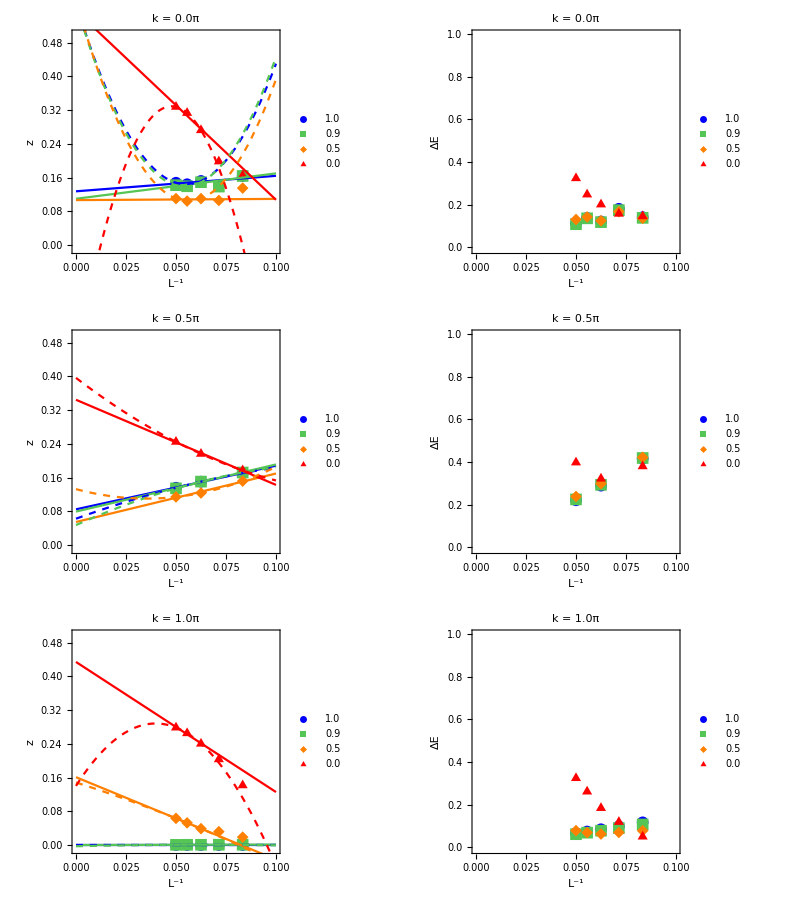

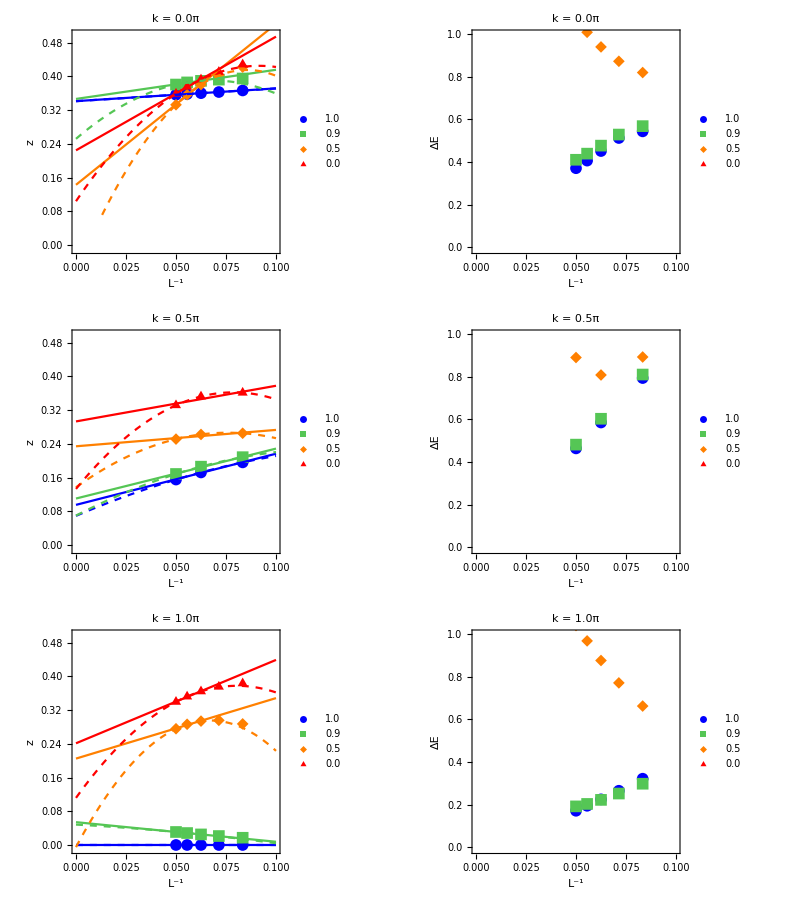

```mathematica
plots={};
qpData=Import["data/qp_J=0.4.json","RawJSON"];
qpds1=Dataset[qpData]
AppendTo[plots,makePlots[qpds1]];
qpData=Import["data/qp_J=1.0.json","RawJSON"];
qpds2=Dataset[qpData]
AppendTo[plots,makePlots[qpds2]];
Grid[plots[[1]],Spacings->{Automatic,2}]
Grid[plots[[2]],Spacings->{Automatic,2}]
```